## Triangular distribution

```mathematica
g=-(b/J) x+b
Integrate[g,{x,0,J}]
```

b-(b x)/J

(b J)/2

```mathematica
f=-((2/J)/J)*x+2/J
Integrate[f,{x,0,J}]==1
EV=Integrate[x f,{x,0,J}]
Var=Integrate[(x-EV)^2f,{x,0,J}]
```

2/J-(2 x)/J^2

True

J/3

J^2/18

```mathematica
meanData=2.79164
varData=10.97915
```

2.79164

10.9792

```mathematica
Solve[EV==meanData]
```

{{J→8.37492}}

8.37492

0.238808-0.0285147 x

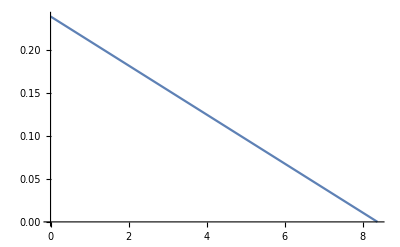

```mathematica
J=8.374920000000001
f=-((2/J)/J)*x+2/J
Plot[f,{x,0,J}]
```

```mathematica
Integrate[f,{x,6,J}]
```

0.0804149

## Circular Distribution

We now swap to a circular distribution

```mathematica
$Assumptions=r>0
g=Sqrt[r^2-x^2]
A=Integrate[g,{x,0,r}]
k=1/A
f=k*g
```

r>0

√(r^2-x^2)

(π r^2)/4

4/(π r^2)

(4 √(r^2-x^2))/(π r^2)

```mathematica
EV=Integrate[x f,{x,0,r}]
Var=Integrate[(x-EV)^2f,{x,0,r}]
```

(4 r)/(3 π)

1/36 (9-64/π^2) r^2

```mathematica
meanData=2.79164
varData=10.97915
ClearAll[r]
Solve[EV==meanData,r]
```

2.79164

10.9792

{{r→6.57765}}

6.57765

0.0294286 √(43.2654-x^2)

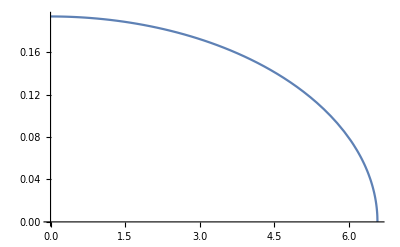

```mathematica
r=6.577646786600558
f=k*g
Plot[f,{x,0,r}]
```

```mathematica
NIntegrate[f,{x,6,r}]
```

0.0308259

## Gamma Distribution

```mathematica
$Assumptions={β>0,α>0}
f=(β^α)/(Gamma[α])x^(α-1)Exp[-β x]
A=Integrate[ f,{x,0,Infinity}]
EV=Integrate[x f,{x,0,Infinity}]
Var=Integrate[(x-EV)^2f,{x,0,Infinity}]
```

{β>0,α>0}

(ⅇ^(-x β) x^(-1+α) β^α)/Gamma[α]

1

α/β

α/β^2

```mathematica
meanData=2.79164
varData=10.97915
ClearAll[β,α]
Solve[{EV==meanData, Var==varData},{β,α}]
Solve[EV==meanData&& Var==varData,{β,α}]
```

2.79164

10.9792

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{β→0.254267,α→0.709823}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{β→0.254267,α→0.709823}}

0.254267

0.709823

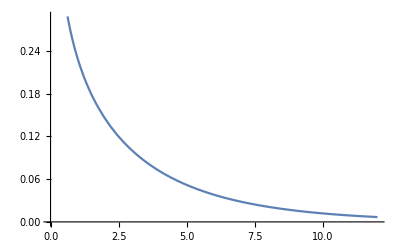

```mathematica
β=0.2542674068575436
α=0.7098230636797931
Plot[f,{x,0,12}]
```

```mathematica
NIntegrate[f,{x,6,Infinity}]
```

0.132508

## Uniform Distribution

```mathematica
$Assumptions={β>0,α>0}
f=update this
A=Integrate[ f,{x,0,Infinity}]
EV=Integrate[x f,{x,0,Infinity}]
Var=Integrate[(x-EV)^2f,{x,0,Infinity}]
```

{β>0,α>0}

(ⅇ^(-x β) x^(-1+α) β^α)/Gamma[α]

1

α/β

α/β^2

```mathematica
meanData=2.79164
varData=10.97915
ClearAll[β,α]
Solve[{EV==meanData, Var==varData},{β,α}]
Solve[EV==meanData&& Var==varData,{β,α}]
```

2.79164

10.9792

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{β→0.254267,α→0.709823}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{β→0.254267,α→0.709823}}

```mathematica
β=0.2542674068575436
α=0.7098230636797931
Plot[f,{x,0,12}]
```

0.254267

0.709823

-Graphics-

```mathematica
NIntegrate[f,{x,6,Infinity}]
```

0.132508